```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

```mathematica
namerun="tretevnocuts";
```

```mathematica
namefolder="2to4_mumuttbar_onlyWeak";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MmumuOW =prova[12];
MttOW =prova[16];


namefolder="2to4_mumuttbar_onlyQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MmumuOQ =prova[12];
MttOQ =prova[16];

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"mllminduecentoOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MmumuOQmllmin200 =prova[12];
MttOQmllmin200 =prova[16];*)
```

```mathematica
namefolder="2to4_mumuttbar";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MmumuWandQ =prova[12];
MttWandQ =prova[16];


namefolder="ZZ_to_tt_massivemu";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttOWfromEVA =prova[8];


namefolder="VVneutral_to_tt_massivemu";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttfromEVA =prova[8];
```

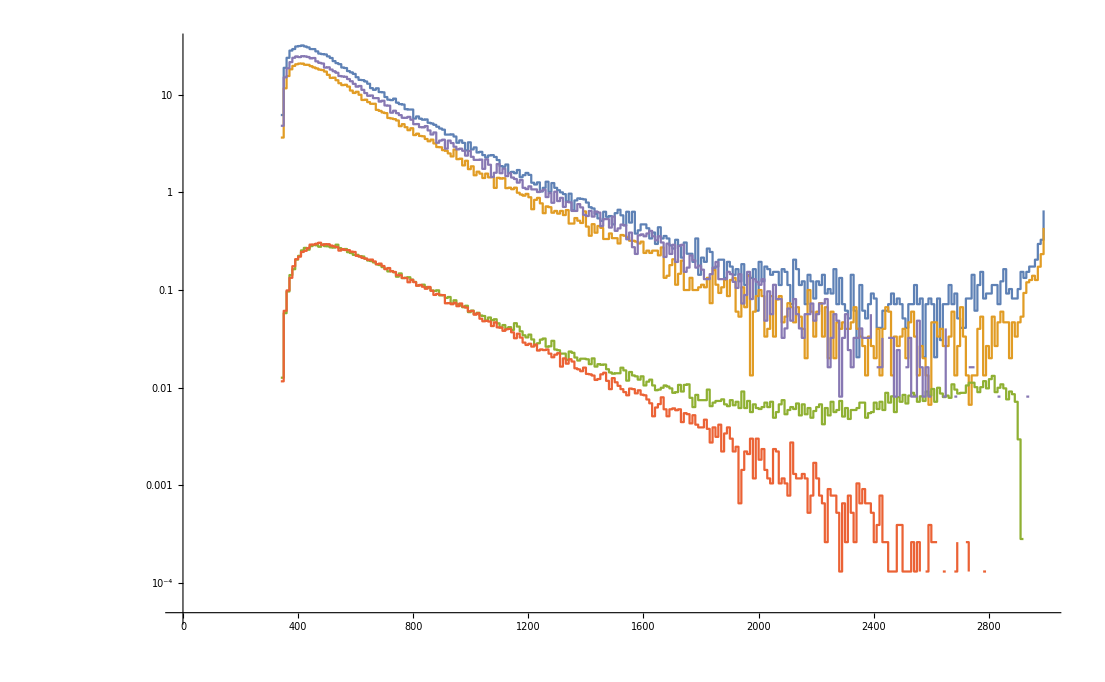

```mathematica
ListLogPlot[{MttWandQ,MttOQ,MttOW,MttOWfromEVA,MttfromEVA},Joined->True,InterpolationOrder->0]
```

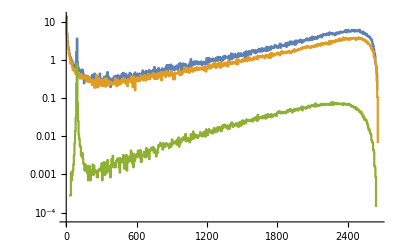

```mathematica
ListLogPlot[{MmumuWandQ,MmumuOQ,MmumuOW},Joined->True,InterpolationOrder->0]
```

```mathematica
namesruns={"unotevnocuts","tretevnocuts","diecitevnocuts"(*,"unotevmllmaxduecento","tretevmllmaxduecento","diecitevmllmaxduecento"*)}
```

{unotevnocuts,tretevnocuts,diecitevnocuts}

```mathematica
{"unotevnocuts","tretevnocuts","diecitevnocuts","unotevmllmaxduecento","tretevmllmaxduecento","diecitevmllmaxduecento"}
```

{unotevnocuts,tretevnocuts,diecitevnocuts,unotevmllmaxduecento,tretevmllmaxduecento,diecitevmllmaxduecento}

```mathematica
Do[

nbintogether=1;



namerun=namesruns[[i]];

subdir="nocuts";


Which[StringMatchQ[namesruns[[i]],"*maxduecento*"],subdir="mllmaxduecento"
];


Which[StringMatchQ[namesruns[[i]],"*uno*"],nbintogether=1,
StringMatchQ[namesruns[[i]],"*tre*"],nbintogether=4,
StringMatchQ[namesruns[[i]],"*dieci*"],nbintogether=10(*,
StringMatchQ[namesruns[[i]],"*cento*"],nbintogether=40*)];

Which[StringMatchQ[namesruns[[i]],"*uno*"],maxrange=25;maxrangeX=1000,
StringMatchQ[namesruns[[i]],"*tre*"],maxrange=30;maxrangeX=3000,
StringMatchQ[namesruns[[i]],"*dieci*"],maxrange=100;maxrangeX=10000(*,
StringMatchQ[namesruns[[i]],"*cento*"],nbintogether=40*)];

maxrangeXmll=maxrangeX;

Which[StringMatchQ[namesruns[[i]],"*maxduecento*"],maxrangeXmll=200
];


namefolder="2to4_mumuttbar_onlyWeak";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOW =joinbin[prova[12],nbintogether];
MttOW =joinbin[prova[16],nbintogether];


If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOWmllmin200 =joinbin[prova[12],nbintogether];
MttOWmllmin200 =joinbin[prova[16],nbintogether]];








namefolder="2to4_mumuttbar_onlyQED";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQ =joinbin[prova[12],nbintogether];
MttOQ =joinbin[prova[16],nbintogether];

If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQmllmin200 =joinbin[prova[12],nbintogether];
MttOQmllmin200 =joinbin[prova[16],nbintogether]];












namefolder="2to4_mumuttbar";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQ =joinbin[prova[12],nbintogether];
MttWandQ =joinbin[prova[16],nbintogether];

If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>StringDrop[namerun,-6]<>"mllminduecentoOK"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQmllmin200 =joinbin[prova[12],nbintogether];
MttWandQmllmin200 =joinbin[prova[16],nbintogether]];











If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],

namefolder="ZZ_to_tt_massivemu";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttOWfromEVA =joinbin[prova[8],nbintogether];


namefolder="VVneutral_to_tt_massivemu";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttfromEVA =joinbin[prova[8],nbintogether];

];



namefolder="2to4_mupemttbar_onlyWeak";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MttOWmue =joinbin[prova[8],nbintogether];







Mmumuplot=ListLogPlot[{MmumuWandQ,MmumuOQ,MmumuOW,MmumuOQmllmin200},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"m(mumu) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeXmll},{0,maxrange}}];
Mmumuplotlinear=ListPlot[{MmumuWandQ,MmumuOQ,MmumuOW,MmumuOQmllmin200},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar(Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"m(mumu) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeXmll},{0,maxrange}}];


If[!StringMatchQ[namesruns[[i]],"*maxduecento*"],

Mttplot=ListLogPlot[{MttWandQ,MttOQ,MttOW,MttOWfromEVA,MttfromEVA ,MttOWmue},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED", "ZZ->tt EVA", "V=Z,a VV->tt EVA","mue->ttmue No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];
Mttplotlinear=ListPlot[{MttWandQ,MttOQ,MttOW,MttOWfromEVA,MttfromEVA,MttOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED", "ZZ->tt EVA", "V=Z,a VV->tt EVA","mue->ttmue No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*5}}];
Mttratio=ListPlot[{rapp[MttOW,MttOWfromEVA],rapp[MttOWmue,MttOWfromEVA] },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar ratio over ZZ->tt EVA",PlotLegends->{"mumu->ttmumu No QED","mue->ttmue No QED"},AxesLabel->{"m(tt) [GeV]","ratio"},PlotRange->{{0,maxrangeX},{0,2}}];


Mttplotmllgt200=ListLogPlot[{MttWandQmllmin200,MttOQmllmin200,MttOWmllmin200,MttOWfromEVA,MttfromEVA,MttOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED", "ZZ->tt EVA", "V=Z,a VV->tt EVA","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];
Mttplotlinearmllgt200=ListPlot[{MttWandQmllmin200,MttOQmllmin200,MttOWmllmin200,MttOWfromEVA,MttfromEVA,MttOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED", "ZZ->tt EVA", "V=Z,a VV->tt EVA","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*5}}];
Mttratiomllgt200=ListPlot[{rapp[MttOWmllmin200,MttOWfromEVA],rapp[MttOWmue,MttOWfromEVA] },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu No QED","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,2}}];


Mttplotmllcutsornot=ListLogPlot[{MttWandQ,MttOQ,MttOW,MttWandQmllmin200,MttOQmllmin200,MttOWmllmin200 ,MttOWmue},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED","mumu->ttmumu mll>200","mumu->ttmumu Only QED mll>200","mumu->ttmumu No QED mll>200","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];

Mttplotlinearmllcutsornot=ListPlot[{MttWandQ,MttOQ,MttOW,MttWandQmllmin200,MttOQmllmin200,MttOWmllmin200,MttOWmue },Joined->True,InterpolationOrder->0,PlotLabel->"ttbar (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED","mumu->ttmumu mll>200","mumu->ttmumu Only QED mll>200","mumu->ttmumu No QED mll>200","mue->ttmue No QED (no mllcut)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*5}}];,









,

Mttplot=ListLogPlot[{MttWandQ,MttOQ,MttOW ,MttOQmllmin200},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];
Mttplotlinear=ListPlot[{MttWandQ,MttOQ,MttOW,MttOQmllmin200},Joined->True,InterpolationOrder->0,PlotLabel->"ttbar (Linear)",PlotLegends->{"mumu->ttmumu","mumu->ttmumu Only QED","mumu->ttmumu No QED"},AxesLabel->{"m(tt) [GeV]","σ[pb]"},PlotRange->{{0,maxrangeX},{0,maxrange*10}}]

];





(*mainpanel=ListLogLogPlot[{mumuttbar,muettbar,WWttbar,VVttbar},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];

ratioinset=ListLogLinearPlot[{rapp[mumuttbar,mumuttbar],rapp[muettbar,mumuttbar],rapp[WWttbar,mumuttbar],rapp[VVttbar,mumuttbar]},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar| ratio over mupmu->ttnunu (all flav)", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ/σ(mupmu->ttnunu)"}];


ratioinset2=ListLogLinearPlot[{rapp[mumuttbar, muettbar],rapp[muettbar, muettbar],rapp[WWttbar, muettbar],rapp[VVttbar, muettbar]},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar| ratio over mupem->ttnumunue", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ/σ(mupem->ttnumunue)"}];*)

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mmumu.pdf",Mmumuplot];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mmumu_linear.pdf",Mmumuplotlinear];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mtt.pdf",Mttplot];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttratio.pdf",Mttratio];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mtt_linear.pdf",Mttplotlinear];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllgt200.pdf",Mttplotmllgt200];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllgt200ratio.pdf",Mttratiomllgt200];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllgt200_linear.pdf",Mttplotlinearmllgt200];


Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllcutsornot.pdf",Mttplotmllcutsornot];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/testmll/"<>subdir<>"/"<>namerun<>"_Mttmllcutsornot_linear.pdf",Mttplotlinearmllcutsornot];



,{i,1,Length[namesruns]}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
StringMatchQ["centoaldofdas","*cento*"]
```

True

```mathematica
(*namefolderoption="2to4_mumuttbar_onlyWeak"*)
(*namefolderoption="2to4_mumuttbar_onlyQED"*)
namefolderoption="2to4_mumuttbar"
```

2to4_mumuttbar

```mathematica
namerun="unotevnocuts";
namefolder=namefolderoption;
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQat1000 =joinbin[prova[12],1];
above200MmumuWandQat1000=Drop[MmumuWandQat1000,42];
Plus@@Map[#[[2]]&,MmumuWandQat1000]
Plus@@Map[#[[2]]&,above200MmumuWandQat1000]
```

30.3763

18.8128

```mathematica
namerun="tretevnocuts";
namefolder=namefolderoption;
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQat3000 =joinbin[prova[12],1];
above20MmumuWandQat3000=Drop[MmumuWandQat3000,6];
above200MmumuWandQat3000=Drop[MmumuWandQat3000,42];
above75MmumuWandQat3000=Drop[MmumuWandQat3000,17];
Plus@@Map[#[[2]]&,MmumuWandQat3000]
Plus@@Map[#[[2]]&,above20MmumuWandQat3000]
Plus@@Map[#[[2]]&,above75MmumuWandQat3000]
Plus@@Map[#[[2]]&,above200MmumuWandQat3000]
```

1021.29

995.151

984.969

969.456

```mathematica
namerun="diecitevnocuts";
namefolder=namefolderoption;
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuWandQat10000 =joinbin[prova[12],1];
above200MmumuWandQat10000=Drop[MmumuWandQat10000,42];
Plus@@Map[#[[2]]&,MmumuWandQat10000]
Plus@@Map[#[[2]]&,above200MmumuWandQat10000]
```

703.098

692.845

```mathematica
namerun="tretevnocuts"
```

tretevnocuts

```mathematica
namefolder="2to4_mumuttbar_onlyQED";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQ =joinbin[prova[12],nbintogether];
MttOQ =joinbin[prova[16],nbintogether];
```

```mathematica
namerun="tretevmllminduecentoOK"
```

tretevmllminduecentoOK

```mathematica
namefolder="2to4_mumuttbar_onlyQED";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
MmumuOQmllover200 =joinbin[prova[12],nbintogether];
MttOQmllover200 =joinbin[prova[16],nbintogether];
```

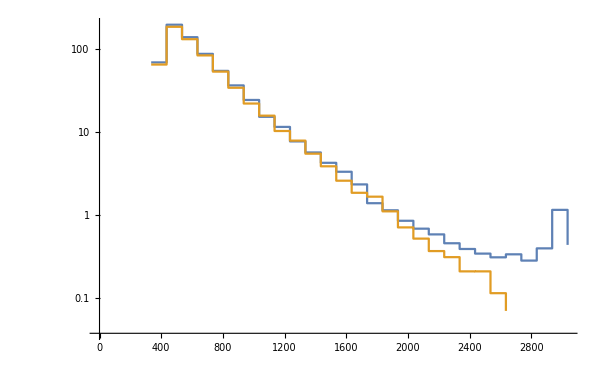

```mathematica
ListLogPlot[{MttOQ,MttOQmllover200},Joined->True,InterpolationOrder->0]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

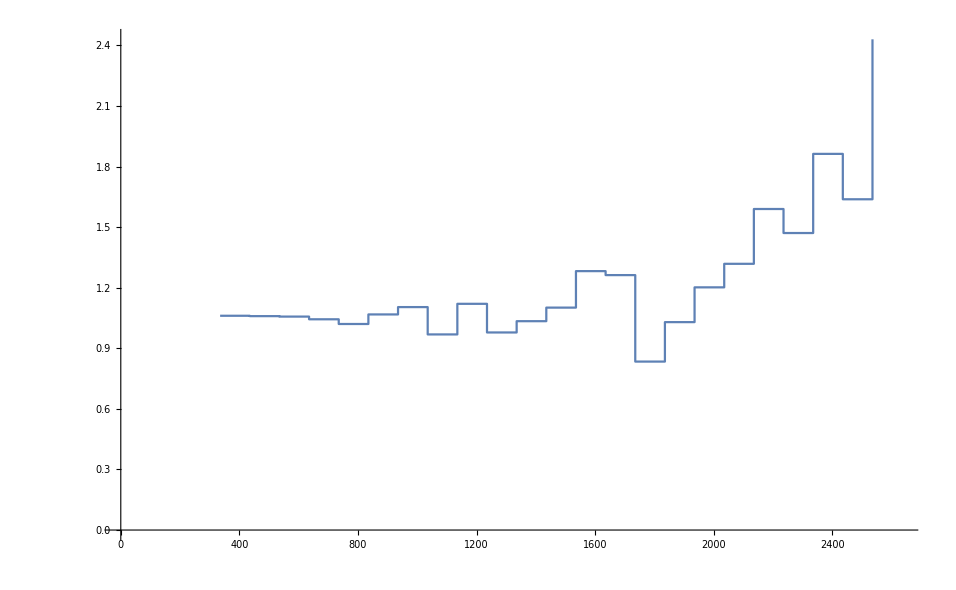

```mathematica
ListPlot[rapp[MttOQ,MttOQmllover200],Joined->True,InterpolationOrder->0]
```

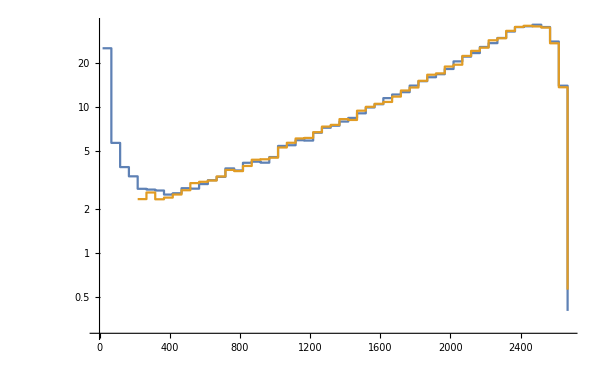

```mathematica
ListLogPlot[{MmumuOQ,MmumuOQmllover200},Joined->True,InterpolationOrder->0]
```